# Day 3 Solutions

## (For Jason’s exercise)

# Easy Exercises

## Exercise Fit

• Define a function GiveFit like FindFit but it instead returns the fully fitted function with the coefficients fully substituted into the fitted function.

Example: if theCoeffs=FindFit[times,a ⅇ^(b x) +c,{a,b,c},x] returns
{a→1.24367×10^-6,b→0.482733,c→0.000500732}
then GiveFit[times,a ⅇ^(b x) +c,{a,b,c},x] should return
0.000500732+1.24367×10^-6 ⅇ^(0.482733 x)

```mathematica
GiveFit[data_List,model_,coefs_,x_]:=
model/.FindFit[data,model,coefs,x]
```

## Exercise Holding...

Create a function children which returns the list of the children of the argument without evaluation. For instance children[h[a,b]]->{a,b} and children[2+2]->{2,2}

```mathematica
SetAttributes[children,HoldAll]
children@a_:=Identity@@ List @@@ Hold@a
```

Or

```mathematica
SetAttributes[children,HoldAll]
children@a_:=List @@Unevaluated @ a
```

Or

```mathematica
SetAttributes[children,HoldAll]
children@f_[a___]:={a}
```

## Exercise BessleJ manipulate

```mathematica
Manipulate[Plot[BesselJ[n,x],{x,0,10}],{n,0,5,1}]
```

Create a simple Manipulate exploring BessleJ[n,x].

## Exercise Cases

Given a list of functions, find the multiplier in the power x of any terms at any level (hint generalized use of cases.) Example input’
{a ⅇ^(-ⅈ x)

coefPowerOfX[{a ⅇ^(-ⅈ x)+3,Sin[x^2],Sin[2^(3 x)],f}]→{-ⅈ,3}

```mathematica
coefPowerOfX[a_]:=Cases[a,f_^(c_ x)->c,∞]
```

```mathematica
coefPowerOfX[{a ⅇ^(-ⅈ x)+3,Sin[x^2],Sin[2^(3 x)],f}]
```

{-ⅈ,3}

## ReplaceDerivatives

Define a function ReplaceDerivatives[expr, replacements] which will replace all derivative terms in expr with the replacements in replacements. For example ReplaceDerivatives[f'[x]+k f''[x],f[x]→x^3] should yield 6 k x+3 x^2

```mathematica
ReplaceDerivatives[expr_,replacements_]:=
Block[{MyDerivative,ans},
ans=expr/.Derivative[n_][f_][x_]:>MyDerivative[n,x,f[x]];
ans=ans/.replacements;
ans/.MyDerivative[n_,x_,func_]:>D[func,{x,n}]
]
```

## RepeatedToIndex

Create a function which will replace every repeated element in a list by it’s index in the list. Example RepeatedToIndex[{a,b,a,c,d,e,c,f,f}] → {1,b,3,4,d,e,7,8,9}

```mathematica
RepeatedToIndex[{a,b,a,c,d,e,c,f,f}]
```

{1,b,3,4,d,e,7,8,9}

```mathematica
RepeatedToIndex[args_List]:=Block[{repeated,reducer},
repeated=First/@Select[Gather @ args,Length@#>1&];
reducer[a_,{i_}]/;MemberQ[repeated,a]:=i;
reducer[a_,{i_}]:=a;
MapIndexed[reducer,args]
]
```

## Orthogonality via Parallel Processing

Create a table verifying the orthogonality of the ChebyshevT polynomials ∫_-1^1 (ChebyshevT[n,x]ChebyshevT[m,x])/(√(1-x^2))ⅆx for n and m running over 1...6 by distributing these in parallel

```mathematica
Table[ParallelSubmit[{m,n},∫_-1^1 (ChebyshevT[m,x]ChebyshevT[n,x])/(√(1-x^2))ⅆx],{m,1,3},{n,1,3}]
```

# Medium Exercises

## Differentation

Implement your own version of partial differentiation, including linearity, chain and product rules.

Add the derivatives of Sin, Cos, Tan, Exp, Log

This is covered in day 2 as well...

```mathematica
MyD[a_+b_,x_]:=MyD[a,x]+MyD[b,x]
MyD[a_ b_,x_]:=a MyD[b,x]+MyD[a,x]b
```

```mathematica
MyD[x_,x_]:=1
MyD[a_^n_Integer,x_]:=n a^(n-1)MyD[a,x]
MyD[a_[f_],x_]:=MyD[a[f],f]MyD[f,x]
```

```mathematica
MyD[Cos[x_],x_]:=-Sin[x]
MyD[Sin[x_],x_]:=-Cos[x]
```

```mathematica
MyD[Exp[f_],x_]:=Exp[f]MyD[f,x]
MyD[Log[f_],x_]:=MyD[f,x]/f
```

```mathematica
MyD[f_,x_]/;FreeQ[f,x]:=0
```

## Resistor Pairings

A power supply stabilizer chip supplies a stable output voltage dependent on two resistances:

```mathematica
Subscript[v, out]==1.22 (Subscript[R, 1]+Subscript[R, 2])/Subscript[R, 2]
```

Typical resistors you can order only come in the following standard values:

```mathematica
OhmT = {10.0,10.2,10.5,10.7,11.0,11.3,11.5,11.8,12.1,12.4,12.7,13.0,13.3,13.7,14.0,14.3,14.7,15.0,15.4,15.8,16.2,16.5,16.9,17.4,17.8,18.2,18.7,19.1,19.6,20.0,20.5,21.0,21.5,22.1,22.6,23.2,23.7,24.3,24.9,25.5,26.1,26.7,27.4,28.0,28.7,29.4,30.1,30.9,31.6,32.4,33.2,34.0,34.8,35.7,36.5,37.4,38.3,39.2,40.2,41.2,42.2,43.2,44.2,45.3,46.4,47.5,48.7,49.9,51.1,52.3,53.6,54.9,56.2,57.6,59.0,60.4,61.9,63.4,64.9,66.5,68.1,69.8,71.5,73.2,75.0,76.8,78.7,80.6,82.5,84.5,86.6,88.7,90.9,93.1,95.3,97.6};
```

1. Write a function closestPair[vout] which will return {vclose, r1, r2} where vclose is the closest voltage to vout and r1 and r2 are the resistors which will produce this close voltage.

```mathematica
closestPair[val_]:=Module[{ratios,minVal},
ratios=Flatten[Outer[{r1,r2}↦{(1.221 (r1+r2))/r2,r1,r2},OhmT,OhmT],1];
minVal=MinimalBy[ratios,Abs[val-First@#]&][[1]];
minVal
]
```

```mathematica
closestPair2[5.14]
```

{5.16028,44.2,13.7}

```mathematica
closestPair[5.14]
```

{5.16028,44.2,13.7}

2. Graph vclose and vout over 5.0V to 5.3V

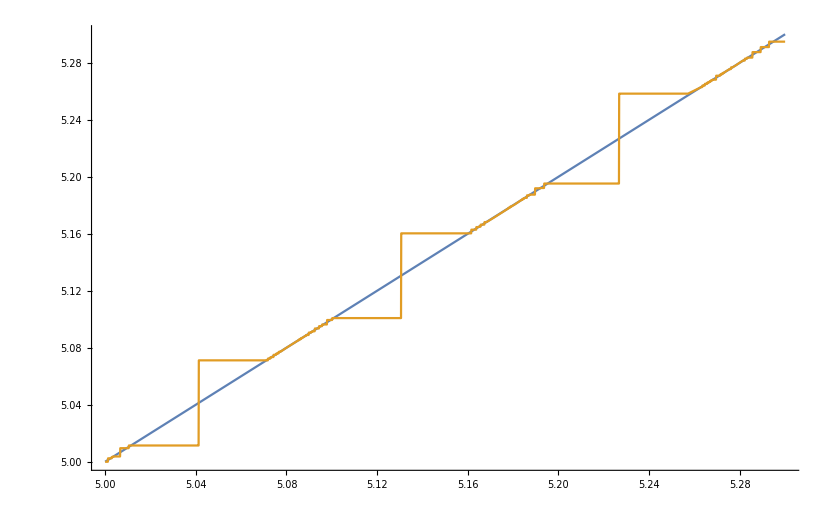

```mathematica
Plot[{val,closestPair[val][[1]]},{val,5.0,5.3}]
```

# Notation Exercises

## Exercise Vector Notation...

Create a notation v_~ to represent Vector[v]

```mathematica
Notation[v__~ ⟺ Vector[v_]]
```

## Exercise Commutator Notation...

Create a notation for [a,b]_c  to represent Commutator[a,b]

```mathematica
Notation[[a_,b_]_c ⟺ Commutator[a_,b_]]
```

```mathematica
a+Commutator[a,b]
```

However there are problems with this notation which we will solve later for instance consider

```mathematica
a+g+Subscript[2 [a,b], c]
```

a+g+(2[a,b])_c

```mathematica
FullForm @ %
```

Plus[a,g,Subscript[2[a,b],c]]

```mathematica
Subscript[f [a,b], c]
```

f[a,b]_c

```mathematica
FullForm @ %
```

Subscript[f[a,b],c]

As one can see the normal function application interpretation is overriding our interpretation. To solve these problems we will use TemplateBoxes which I will talk about early next week.

## Exercise Your own Notation...

Create a notation for some function you use in physics. (There are several things I haven’t explained yet so if you have problems then wait for further lectures, information here.)

# More Challenging

## Diversion: Optional

Do explanation of f[x_,y_:0]:=g[x,y]

```mathematica
coefPowerOfX[a_]:=Cases[a,f_^(c_:0 x)->c,∞]
```

## Exercise: Non commutative multiply

Create a Non-commutative multiply function which distributes over addition, and constants can be factored out.